# imaging moveout approximation

## imaging moveout

```mathematica
Clear["Global`*"]
```

```mathematica
delta=(epslion-eta)/(1+2 eta)
```

(epslion-eta)/(1+2 eta)

```mathematica
p=(1-s)/(v0*√(1+2 delta) √(1+2 eta))
```

(1-s)/(√(1+2 eta) √(1+(2 (epslion-eta))/(1+2 eta)) v0)

```mathematica
z0=Simplify[(1-√(1+2 delta) √(1+2 eta) p v0)/(√(1+2 delta) √(1+2 eta) G p)]
```

(s v0)/(G-G s)

```mathematica
x0=Simplify[(√(1-(1+2 delta) (1+2 eta) p^2 v0^2))/(G p √(1-2 (1+2 delta) eta p^2 v0^2)),√(1+2 eta)>0&&√(1+2 epslion)>0]
```

-(√(-(1+2 epslion) (1+2 eta) (-2+s) s) v0)/(G (-1+s) √(1-2 eta (-2+s) s))

## for t0

```mathematica
vn0=Sqrt[1+2*delta]*v0;
```

```mathematica
R1=1-(1+2*eta)*p^2*vn0^2;
```

```mathematica
R2=1-2*eta*p^2*vn0^2;
```

```mathematica
p1=Simplify[Sqrt[R1/R2]];
```

```mathematica
p2=Simplify[Log[(Sqrt[R1]+Sqrt[R2])/(Sqrt[1+2 delta]*p*v0)]];
```

```mathematica
p3=Simplify[1/2*Sqrt[(1+2*eta)/(2*eta)]*Log[1+4*eta*R1-2*Sqrt[2*eta*(1+2*eta)*R1*R2]]];
```

```mathematica
t0=Simplify[(p1+p2+p3)/G,√(1+2 eta)>0&&√eta>0&&√(1+2 epslion)>0]
```

(4 √(((1+2 eta) (-2+s) s)/(-1+2 eta (-2+s) s))+4 Log[-(√(-(1+2 eta) (-2+s) s)+√(1-2 eta (-2+s) s))/(-1+s)]+√2 √(2+1/eta) Log[1-4 eta (-2+s) s-2 √2 √(eta (-2+s) s (-1+2 eta (-2+s) s))])/(4 G)

```mathematica
param={v0->2,G->1.5,epslion->0.22,eta->0.1}
```

{v0→2,G→1.5,epslion→0.22,eta→0.1}

```mathematica
Zp=Simplify[(v0 (-p^2 v0^2-ⅇ^(4 G t0) p^2 v0^2+2 ⅇ^(2 G t0) (-2+p^2 v0^2)-2 ⅇ^(G t0) (-1+√(1-p^2 v0^2))+2 ⅇ^(3 G t0) (1+√(1-p^2 v0^2))))/(G (p^2 v0^2+ⅇ^(4 G t0) p^2 v0^2+ⅇ^(2 G t0) (4-2 p^2 v0^2))),√(1+2 eta)>0&&√eta>0&&√(1+2 epslion)>0];
```

```mathematica
Xp=(Sqrt[1-p^2*v0^2]-Sqrt[1-p^2*(v0+G*Zp)^2])/(p*G);
```

```mathematica
Dx=x0-Xp;
```

```mathematica
zp=Zp/.param;
```

```mathematica
dx=Dx/.param;
```

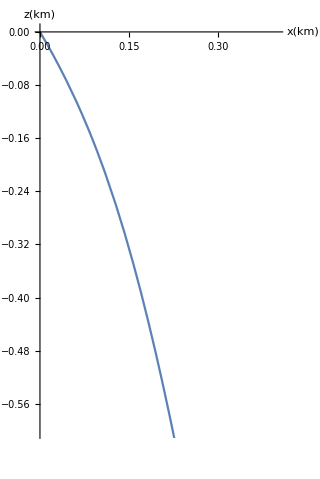

```mathematica
ParametricPlot[{dx,-zp},{s,0,0.9},PlotRange->{{0,0.4},{-0.6,0}},AxesLabel->{Style["x(km)",FontSize->20],Style["z(km)",FontSize->20]}]
```

```mathematica
k1=Simplify[√2 √epslion]
```

√2 √epslion

```mathematica
k2=Simplify[-((1+2 epslion) G)/(2 √2 √epslion v0)]
```

-((1+2 epslion) G)/(2 √2 √epslion v0)

```mathematica
k3=Simplify[((1+2 epslion) (-eta+epslion (3+4 eta)) G^2)/(6 √2 epslion^(3/2) (1+2 eta) v0^2)]
```

((1+2 epslion) (-eta+epslion (3+4 eta)) G^2)/(6 √2 epslion^(3/2) (1+2 eta) v0^2)

```mathematica
k4=Simplify[((1+2 epslion) (1-2 eta-16 epslion^2 (1+eta)+2 epslion (1+2 eta)) G^3)/(32 √2 epslion^(5/2) (1+2 eta) v0^3)]
```

((1+2 epslion) (1-2 eta-16 epslion^2 (1+eta)+epslion (2+4 eta)) G^3)/(32 √2 epslion^(5/2) (1+2 eta) v0^3)

```mathematica
X1=k1*zzp/.param;
```

```mathematica
X2=k1*zzp+k2*zzp^2/.param;
```

```mathematica
X3=k1*zzp+k2*zzp^2+k3*zzp^3/.param;
```

```mathematica
X4=k1*zzp+k2*zzp^2+k3*zzp^3+k4*zzp^4/.param;
```

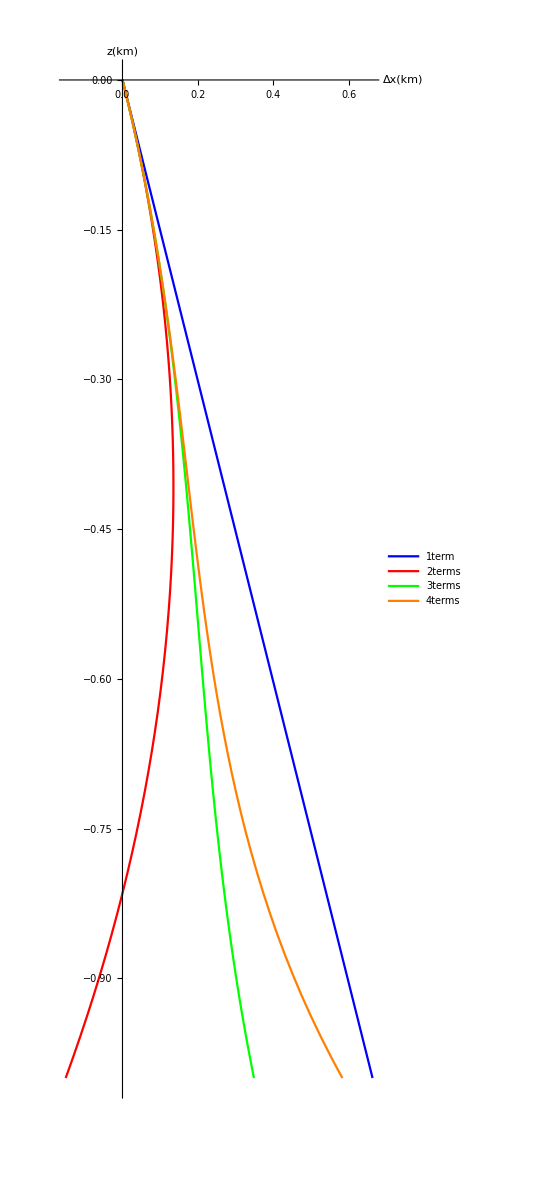

```mathematica
A1=ParametricPlot[{{X1,-zzp},{X2,-zzp},{X3,-zzp},{X4,-zzp}},{zzp,0,1},PlotRange->{{0,0.4},{0,-1}},AspectRatio->3,PlotLegends->Placed[{"1term","2terms","3terms","4terms"},Right],AxesLabel->{Style["Δx(km)",FontSize->15],Style["z(km)",FontSize->15]},PlotStyle->{Blue,Red,Green,Orange}]
```

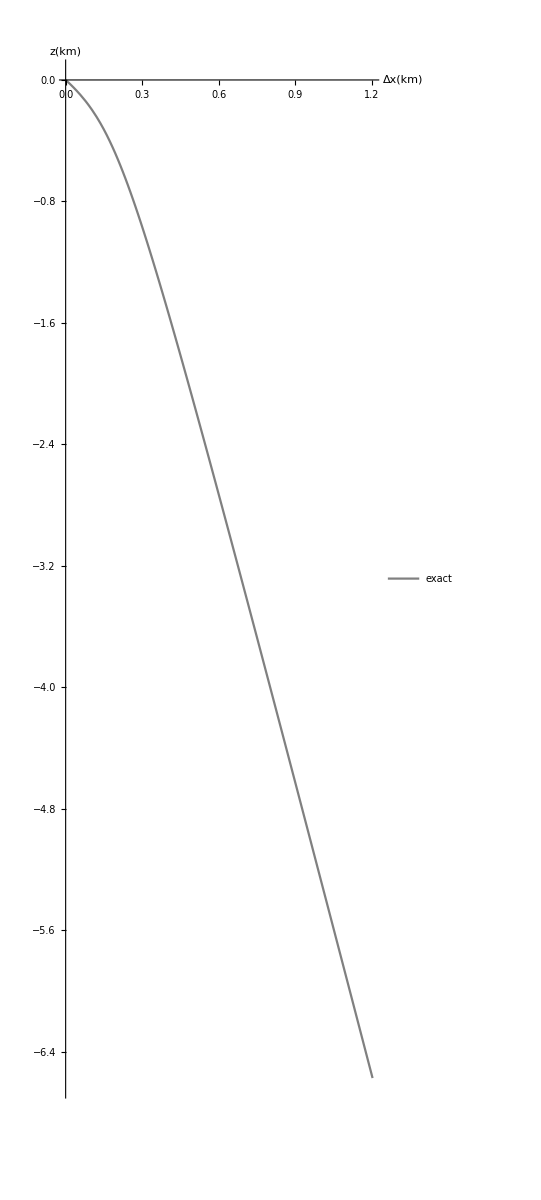

```mathematica
A2=ParametricPlot[{dx,-zp},{s,0,0.8},PlotRange->{{0,0.4},{0,-1}},AspectRatio->3,PlotLegends->Placed[{"exact"},Right],AxesLabel->{Style["Δx(km)",FontSize->15],Style["z(km)",FontSize->15]},PlotStyle->{Gray}]
```

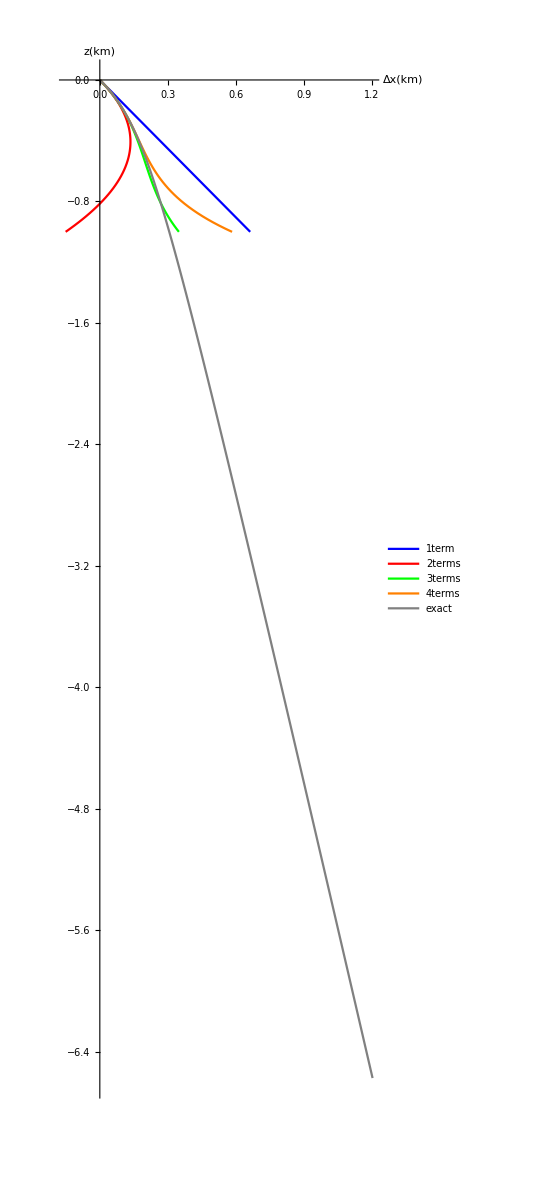

```mathematica
Show[A1,A2]
```

```mathematica
X11=k1*zp/.param;
```

```mathematica
X22=k1*zp+k2*zp^2/.param;
```

```mathematica
X33=k1*zp+k2*zp^2+k3*zp^3/.param;
```

```mathematica
X44=k1*zp+k2*zp^2+k3*zp^3+k4*zp^4/.param;
```

#### size 225

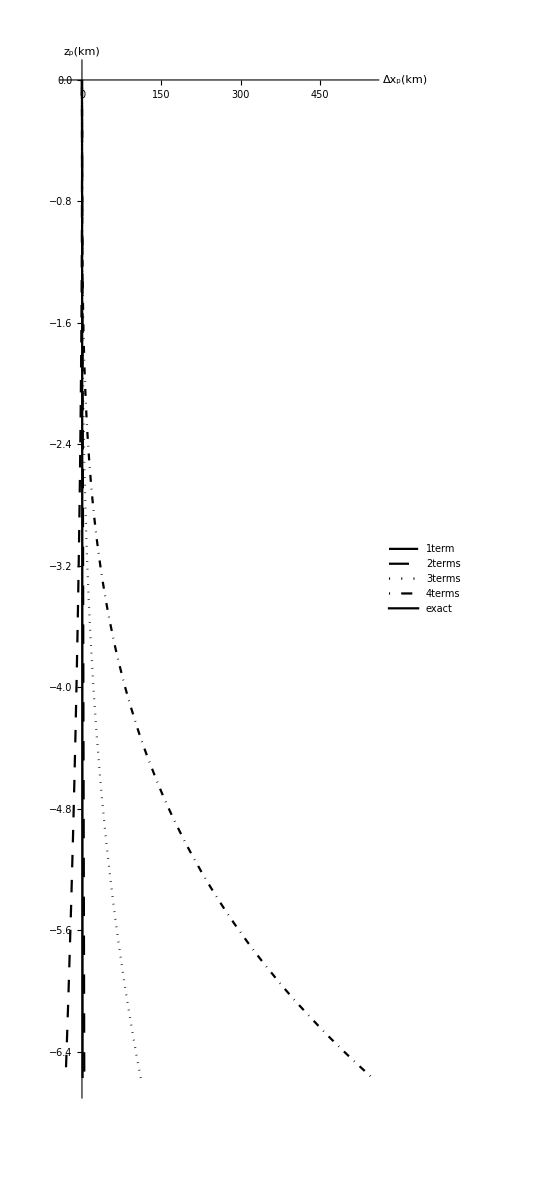

```mathematica
ParametricPlot[{{X11,-zp},{X22,-zp},{X33,-zp},{X44,-zp},{dx,-zp}},{s,0,0.8},PlotRange->{{0,0.4},{0,-1}},AspectRatio->3,PlotLegends->Placed[{"1term","2terms","3terms","4terms","exact"},Right],AxesStyle->Black,AxesLabel->{Style["Δx_p(km)",Black,FontSize->15],Style["z_p(km)",Black,FontSize->15]},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Dashing[Medium],Black,Thick],Directive[Black,Dotted,Thick],Directive[Black,DotDashed,Thick],Directive[Black,Thick]}]
```

## error function

```mathematica
dif1=dx-X11;
```

```mathematica
dif2=dx-X22;
```

```mathematica
dif3=dx-X33;
```

```mathematica
dif4=dx-X44;
```

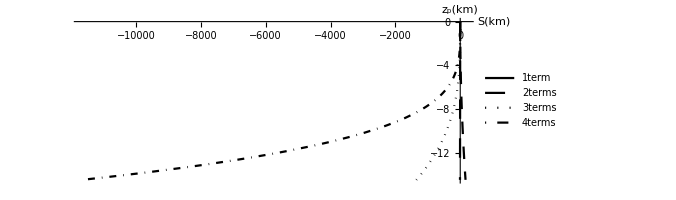

```mathematica
ParametricPlot[{{dif1,-zp},{dif2,-zp},{dif3,-zp},{dif4,-zp}},{s,0,0.9},PlotRange->{{-0.3,0.3},{0,-1}},PlotLegends->Placed[{"1term","2terms","3terms","4terms"},Right],AxesStyle->Black,AxesLabel->{Style["S(km)",Black,FontSize->15],Style["z_p(km)",Black,FontSize->15]},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Dashing[Medium],Black,Thick],Directive[Black,Dotted,Thick],Directive[Black,DotDashed,Thick]}]
```